{0.,0.479426}

{0.,0.479426}

sin的计算时间为：0. s

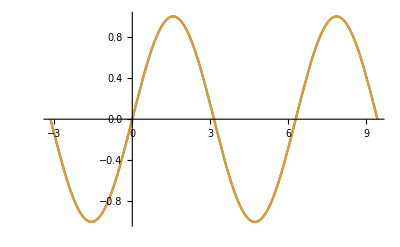
{0.03125,-Graphics-}

```mathematica
(*利用泰勒公式对Sin(x)在x=Pi处进行展开，再利用Sin(x)的周期性拓展到整个实数域*)
sin[x_]:=Module[{y,result,u},
y=Series[Sin[z],{z,Pi,20}] //Normal;
u=N[x-Floor[x/(2*Pi)]*2*Pi];
result=N[y/.z->u];
Return[result];
];
sintime=Timing[N[sin[1/2]]]
N[Sin[1/2]]//Timing
Print["sin的计算时间为：",sintime[[1]]," s"];
Plot[{sin[x],Sin[x]},{x,-Pi,3*Pi}]//Timing
```

{0.,0.523599}

{0.,0.523599}

sin的计算时间为：0. s

用牛顿迭代法方法求解arcsin的计算时间为：0. s

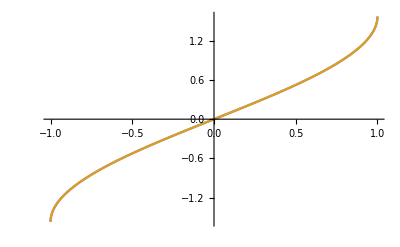
{0.015625,-Graphics-}

{0.,0.523599}

{0.,0.523599}

用Taylor方法求解arcsin的计算时间为：0. s

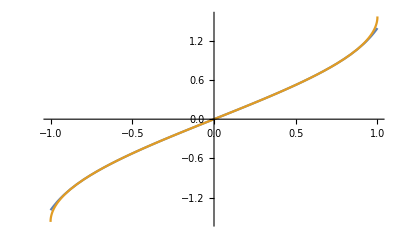
{0.,-Graphics-}

```mathematica
(*方法一：利用牛顿迭代法求解x=Sin(y)的根，这种方法在x->-1和1时仍然能保持较好的精度，速度会相对慢一些*)
arcsin[x_]:=Module[{tol=0.000001,maxIter=100000,x0=0,i=0},If[-1≤x≤1,
If[x==-1 ,Return[-Pi/2]];
If[x==   1,Return[    Pi/2]];
While[i<maxIter&&Abs[Sin[x0]-x]>tol,x0=x0-(Sin[x0]-x)/Cos[x0];i++];
Return[N[x0]];
,
Print["Please input a number between -1 and 1"];
Return[$Failed];

];
];
arcsintime=Timing[arcsin[1/2]]
N[ArcSin[1/2]]//Timing
Print["sin的计算时间为：",arcsintime[[1]]," s"];
Print["用牛顿迭代法方法求解arcsin的计算时间为：",arcsintime[[1]]," s"];
Plot[{arcsin[x],ArcSin[x]},{x,-1,1}]//Timing

(*方法二：对Arcsin(x)做Taylor展开，这种方法在x->-1和1时精度较低，速度会相对快一些*)
arcsin[x_]:=Module[{y,result},
y=Series[ArcSin[z],{z,0,20}] //Normal;
result=N[y/.z->x];
Return[result];
];
arcsintimetl=Timing[arcsin[1/2]]
N[ArcSin[1/2]]//Timing
Print["用Taylor方法求解arcsin的计算时间为：",arcsintimetl[[1]]," s"];
Plot[{arcsin[x],ArcSin[x]},{x,-1,1}]//Timing
```

{0.,1.56689}

{0.,1.56689}

用牛顿迭代方法求解arctan的计算时间为：0. s

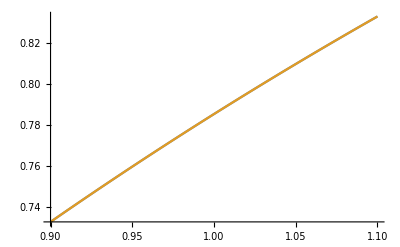
{0.,-Graphics-}

{0.,1.56689}

{0.,1.56689}

用Taylor方法求解arctan的计算时间为：0. s

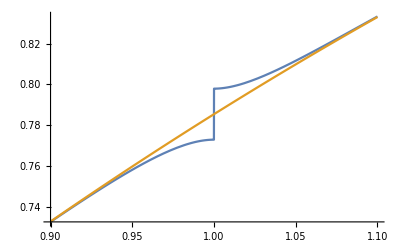
{0.0625,-Graphics-}

```mathematica
(*如何解决当Abs[x]很大时拟合不精确的问题？*)
(*利用x>0时，Arctan(x)+Arctan(1/x)=Pi/2；利用x<0时，Arctan(x)+Arctan(1/x)=-Pi/2*)

(*方法一：利用牛顿迭代法求解x=Arctan(y)的根，这种方法在x->-1和1时仍然能保持较好的精度*)
arctan[x_]:=Module[{x0=0,tol=0.000001,maxIter=1000000,i=0},
If[x≥0,
If[x≤1,
While[i<maxIter&&Abs[Tan[x0]-x]>tol,x0=x0-(Tan[x0]-x)/(Sec[x0]*Sec[x0]);i++];
Return[N[x0]];,
While[i<maxIter&&Abs[Tan[x0]-1/x]>tol,x0=x0-(Tan[x0]-1/x)/(Sec[x0]*Sec[x0]);i++];
Return[N[Pi/2-x0]];
],
If[x≥-1,
While[i<maxIter&&Abs[Tan[x0]-x]>tol,x0=x0-(Tan[x0]-x)/(Sec[x0]*Sec[x0]);i++];
Return[N[x0]];,
While[i<maxIter&&Abs[Tan[x0]-1/x]>tol,x0=x0-(Tan[x0]-1/x)/(Sec[x0]*Sec[x0]);i++];
Return[N[-Pi/2-x0]];
];
];
];
arctantime=Timing[arctan[256]]
N[ArcTan[256]]//Timing
Print["用牛顿迭代方法求解arctan的计算时间为：",arctantime[[1]]," s"];
Plot[{arctan[x],ArcTan[x]},{x,0.9,1.1}]//Timing

(*方法二：对Arctan(x)做Taylor展开，这种方法在x->-1和1时精度较低*)
arctan[x_]:=Module[{y,result,u},
y=Series[ArcTan[z],{z,0,40}]//Normal;
If[x≥0,
If[x≤1,
x0=y/.z->x;Return[N[x0]];,
x0=y/.z->1/x;Return[N[Pi/2-x0]];
],
If[x≥-1,
x0=y/.z->x;Return[N[x0]];,
x0=y/.z->1/x;Return[N[-Pi/2-x0]];
];
];
];
arctantimetl=Timing[arctan[256]]
N[ArcTan[256]]//Timing
Print["用Taylor方法求解arctan的计算时间为：",arctantimetl[[1]]," s"];
Plot[{arctan[x],ArcTan[x]},{x,0.9,1.1}]//Timing
```